```mathematica
k = 12;
h = 0.16;

df[x_] := -k*x
f[0.0] = 1;
f[t_] := f[t-h] + df[f[t-h]]*h

g[0.0] = 1;
g[t_] := g[t-h] / (1 + h*k)

Slider[Dynamic[k], {0, 50}]
Slider[Dynamic[h], {0.05, 1}]

Dynamic[Show[Plot[E^(-k*t), {t, 0, 1}, PlotRange->{-1, 1}], DiscretePlot[{f[t], g[t]}, {t, 0, 1, h}, Joined->True, PlotRange->{-1, 1}]]]
```

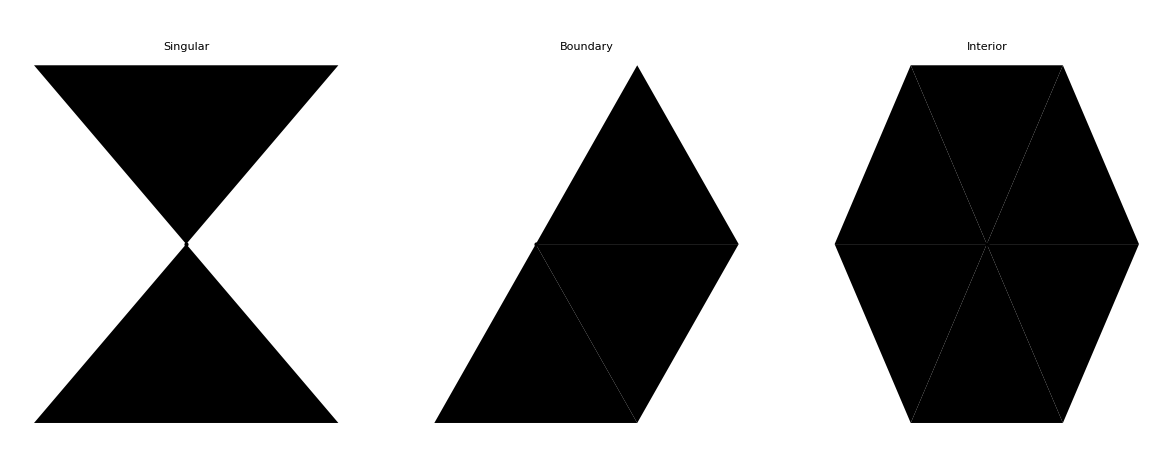

/Users/miles/Kiln/projects/fem/Figures.pdf

```mathematica
apex = {1/2, Sqrt[3]/2};
tri = {{0,0}, {1,0}, apex};
style = {FaceForm[None],EdgeForm[Blue],AbsolutePointSize[8]};

fig = GraphicsRow[{
Graphics[{Polygon[tri], Rotate[Polygon[tri], 180Degree, apex],Point[apex]},PlotLabel->"Singular", BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex], Point[apex]},PlotLabel->"Boundary",BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex],
Rotate[Polygon[tri],180Degree, apex],
Rotate[Polygon[tri],240Degree, apex],
Rotate[Polygon[tri],300Degree, apex] ,Point[apex]},PlotLabel->"Interior", BaseStyle->style]}]

Export[FileNameJoin[{NotebookDirectory[], "figures.pdf"}],fig]
```